## Assignment 1

1. For the period shift map of the pendulum with oscillating suspension point treated in Section 3.4.F of the notes (and studied in the lab classes) plot, in the parameter space (α,k):
	1.a  the first few instability tongues of the lower fixed point z_=(0,0)
	1.b the stability region (regions?) of the upper fixed point z_+ = (π,0)

```mathematica
(*This DS has two fix points （in convenience of typing I denote z0 and z1 instead z_):*)
z0={0,0}; z1={π,0};
```

### 1. a the first few instability tongues of the lower fixed point z0 = (0, 0)

```mathematica
(*Solving the Lagrangian equations, we may find the expression for x(namely, θ) and v.
Since this system is time-dependent, we consider its linearization at z0=(0,0) in the (quotient) extended phase space , and try to find the Jacobian matrix Ψ'(z0) by solving its linearization: *)
XL0[{α_,k_}][{x_,v_,t_}]:={v,-(α^2-k Cos[t])x,1}
(*where α and k are parameters. *)
```

```mathematica
(*Define the Runge-Kutta method for XL:*)
Algo0[αk_,h_][xvt_]:=xvt+h XL0[αk][xvt+h/2 XL0[αk][xvt]]
Algo0[{αk[[1]],αk[[2]]},h][{xvt[[1]],xvt[[2]],xvt[[3]]}]
```

Part::partd: Part specification αk⟦1⟧ is longer than depth of object.

Part::partd: Part specification αk⟦2⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h xvt⟦1⟧ (-αk⟦1⟧^2+Cos[xvt⟦3⟧] αk⟦2⟧)),xvt⟦2⟧+h (xvt⟦1⟧+1/2 h xvt⟦2⟧) (-αk⟦1⟧^2+Cos[h/2+xvt⟦3⟧] αk⟦2⟧),h+xvt⟦3⟧}

```mathematica
Algo0=Compile[{{αk,_Real,1},h,{xvt,_Real,1}},
{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h xvt⟦1⟧ (-αk⟦1⟧^2+Cos[xvt⟦3⟧] αk⟦2⟧)),xvt⟦2⟧+h (xvt⟦1⟧+1/2 h xvt⟦2⟧) (-αk⟦1⟧^2+Cos[h/2+xvt⟦3⟧] αk⟦2⟧),h+xvt⟦3⟧}];
```

```mathematica
(*Using Runge-Kutta, we can find the flow of XL:*)
Sol0=Compile[{{αk,_Real,1},ndiv,{xv,_Real,1}},
Take[Nest[Algo0[αk,(2π)/ndiv,#]&,Append[xv,0],ndiv],2]];
(*this is the flow attained by Runge-Kutta with stepsize=(2π)/ndiv and starting point at {x,v}. *)
```

```mathematica
(*To define the (in)stability of (0,0), we need to look into the eigenvalues of the Jacobian matrix Ψ'(0,0).
It can be deduced through some calculations that the matrix can be desomstrated as follows: *)
PML0[αk_,ndiv_]:={Sol0[αk,ndiv,{1,0}],Sol0[αk,ndiv,{0,1}]}
```

```mathematica
(*The Legendre transformation of this Lagrangian system implies that 1=det|Ψ'(z_)|=Subscript[λ, 1]·Subscript[λ, 2]. 
If z_- is unstable, then (WLOG) |Subscript[λ, 1]| < 1 < |Subscript[λ, 2]|. 
We look into the trace of the Jacobian with each (α,k): *)
Tr0[αk_,ndiv_]:={αk, Abs[Tr[PML0[αk,ndiv]]]}
```

```mathematica
(*Generate a random (α,k) in rgxrgy (which are the range of x and y coordinates of the points respectively), with stepsize of Runge-Kutta=(2π)/ndiv: *)
RTr0[rgx_,rgy_,ndiv_]:=Tr0[{RandomReal[rgx],RandomReal[rgy]},ndiv]
```

```mathematica
(*Select the (α,k)'s that makes z_- unstable, with precision=prec: *)
crTr[prec_][el_]:=el[[2]]>2+prec
```

```mathematica
(*Demonstrat the points: *)
PlInstTr[lst_,prec_,rgx_,rgy_]:=ListPlot[Transpose[Select[lst,crTr[prec]]][[1]],PlotRange->{rgx,rgy}]
```

```mathematica
(*Generates 1000 random (α,k)'s in rg0x×rg0y, with same stepsize: *)
rg0x={0,3};rg0y={0,7};
pts0=Table[RTr0[rg0x,rg0y,100],50000];
```

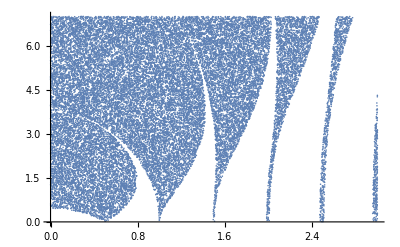

```mathematica
PlInstTr[pts0,-.001,rg0x,rg0y]
```

```mathematica
(*And the picture shows that the instability tongues appears to be cusps at points (n/2,0). The "width" of the cusps decrease as n increases. *)
```

### 1.b the stability region (s) of the upper fixed point z_+ = (π,0)

```mathematica
(*Similar to the former case, we need to look into the Jacobian Ψ'(z_+). 
Similarly define the functions: *)
```

```mathematica
XL1[{α_,k_}][{x_,v_,t_}]:={v,(α^2-k Cos[t])x,1}
Algo1[αk_,h_][xvt_]:=xvt+h XL1[αk][xvt+h/2 XL1[αk][xvt]]
Algo1[{αk[[1]],αk[[2]]},h][{xvt[[1]],xvt[[2]],xvt[[3]]}]
```

Part::partd: Part specification αk⟦1⟧ is longer than depth of object.

Part::partd: Part specification αk⟦2⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h xvt⟦1⟧ (αk⟦1⟧^2-Cos[xvt⟦3⟧] αk⟦2⟧)),xvt⟦2⟧+h (xvt⟦1⟧+1/2 h xvt⟦2⟧) (αk⟦1⟧^2-Cos[h/2+xvt⟦3⟧] αk⟦2⟧),h+xvt⟦3⟧}

```mathematica
Algo1=Compile[{{αk,_Real,1},h,{xvt,_Real,1}},
{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h xvt⟦1⟧ (αk⟦1⟧^2-Cos[xvt⟦3⟧] αk⟦2⟧)),xvt⟦2⟧+h (xvt⟦1⟧+1/2 h xvt⟦2⟧) (αk⟦1⟧^2-Cos[h/2+xvt⟦3⟧] αk⟦2⟧),h+xvt⟦3⟧}];
```

```mathematica
Sol1=Compile[{{αk,_Real,1},ndiv,{xv,_Real,1}},
Take[Nest[Algo1[αk,(2π)/ndiv,#]&,Append[xv,0],ndiv],2]];
```

```mathematica
PML1[αk_,ndiv_]:={Sol1[αk,ndiv,{1,0}],Sol1[αk,ndiv,{0,1}]}
```

```mathematica
Tr1[αk_,ndiv_]:={αk, Abs[Tr[PML1[αk,ndiv]]]}
```

```mathematica
rg1x={0,1.5}; rg1y={0,6};
```

```mathematica
RTr1[rgx_,rgy_,ndiv_]:=Tr1[{RandomReal[rgx],RandomReal[rgy]},ndiv]
```

```mathematica
(*Since we want the stability region(s) of z_+, we need |Subscript[λ, 1]|=1=|Subscript[λ, 2]|, and this implies tr(Ψ'(z_+))=Subscript[λ, 1]+Subscript[λ, 2]<=2: *)
crTr1[prec_][el_]:=el[[2]]<2+prec
```

```mathematica
PlInstTr1[lst_,prec_,rgx_,rgy_]:=ListPlot[Transpose[Select[lst,crTr1[prec]]][[1]],PlotRange->{rgx,rgy}]
```

```mathematica
rg1x={0,10}; rg1y={0,20};
pts1=Table[RTr1[rg1x,rg1y,50],100000];
(*Here I want more points so I am reducing the iteration steps of Runge-Kutta. *)
```

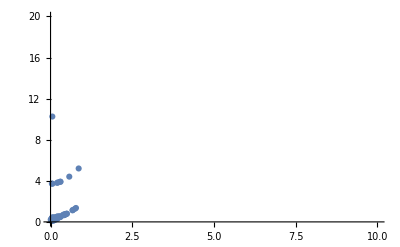

```mathematica
PlInstTr1[pts1,.001,rg1x,rg1y]
```

```mathematica
(*Shrink the intervals to cut out the blank spaces: *)
rg11x={0,1.5}; rg11y={0,7};
pts1=Table[RTr1[rg11x,rg11y,100],50000];
```

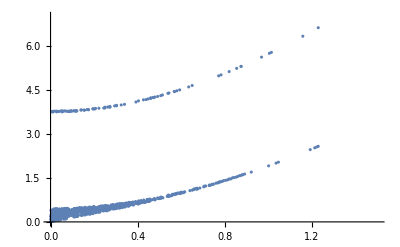

```mathematica
PlInstTr1[pts1,.0001,rg11x,rg11y]
```

```mathematica
(*It has already been discussed during the lecture that, when k=0, it is only when α=0 that it can possibly be stable. 
Yet I tried to figure out what happened when α=0, but the ODE seemed impossible to solve and ended up with no meaningful computation. *)
```